## A002648: A variant of the cuban primes: primes p = (x^3 - y^3)/(x - y) where x = y + 2.

### MATHEMATICA PROGRAM:

```mathematica
Select[Table[3n^2+1,{n,0,700}],PrimeQ] (* Vincenzo Librandi, Dec 02 2011 *)
```

{13,109,193,433,769,1201,1453,2029,3469,3889,4801,10093,12289,13873,18253,20173,21169,22189,28813,37633,43201,47629,60493,63949,65713,69313,73009,76801,84673,106033,108301,112909,115249,129793,139969,142573,147853,169933,172801,178609,181549,193549,209089,221953,238573,245389,259309,270001,273613,280909,284593,299569,307201,326701,342733,355009,363313,367501,397489,410701,415153,424129,433201,534253,544429,549553,565069,596749,618349,640333,645889,685453,720301,762049,786433,823729,842701,940801,961069,967873,995329,1009201,1016173,1037233,1094449,1108993,1116301,1138369,1145773,1190701,1267501,1291009,1322689,1403569,1411789,1436593,1444909}

### Formula:

a(n) = 3*A111051(n)^2 + 1.  - Paul F. Marrero Romero, Nov  03  2023

### Plot section:

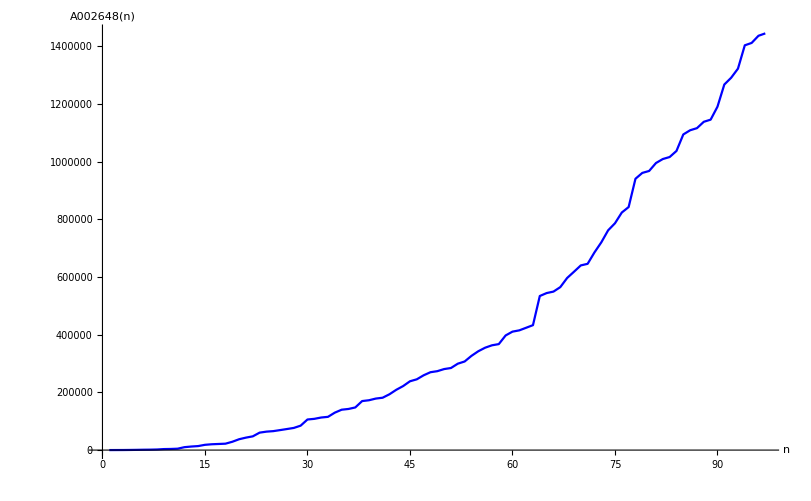

```mathematica
ListPlot[ Select[3*Range[0,701]^2 + 1, PrimeQ], Joined->True, PlotStyle-> Blue, AxesLabel->{"n","A002648(n)"}, LabelStyle->Directive[Black,Bold]]
```

### References:

N. J. A. Sloane, A variant of the cuban primes: primes p = (x^3 - y^3)/(x - y) where x = y + 2., Entry A002648 in The On-Line Encyclopedia of Integer Sequences, https://oeis.org/A002648